```mathematica
Remove["Global`*"]
```

```mathematica
e = 0.000001;
```

```mathematica
(* Points of the example problem *)
```

```mathematica
npoints = 8;
sp[1] = {0.50, 0.50, 0.50};
sp[2] = {-0.50, 0.50, 0.50};
sp[3] = {-0.50, -0.50, 0.50};
sp[4] = {0.50, -0.50, 0.50};
sp[5] = {0.50, 0.50, -0.50};
sp[6] = {-0.50, 0.50, -0.50};
sp[7] = {-0.50, -0.50, -0.50};
sp[8] = {0.50, -0.50, -0.50};
```

```mathematica
Do[
sn[i] = sp[i]/Norm[sp[i]],
{i, npoints}
]
```

```mathematica
sn[1] = {-1.00, -1.00, 1.00};
sn[1] = sn[1] / Norm[sn[1]];
```

```mathematica
(* Octree leaf nodes *)
Do[
oc[i] = sp[i]/2,
{i,npoints}
]
```

```mathematica
ow = 1/2;
```

```mathematica
(* Node funcitons *)
```

```mathematica
points = Table[sp[i], {i,npoints}];
```

```mathematica
Show[
Table[Graphics3D[Arrow[{sp[i], sp[i]+sn[i]*0.20}]],{i,npoints}],
ListPointPlot3D[points, AspectRatio->1],
ListPointPlot3D[Table[oc[i],{i,npoints}] ]

]
```

-Graphics3D-

```mathematica
F[q_]:=If[Abs[q[[1]]]<π/2 &&Abs[q[[2]]]<π/2 && Abs[q[[3]]]<π/2 ,(2 π^(-3/2)*(1-1/2 qᵀ.q)),0.00]
```

```mathematica
Plot3D[{F[{x,y,0.00}], 2 π^(-3/2)*(Cos[x]*Cos[y]*Cos[0.00])}, {x,-π/2,π/2}, {y,-π/2, π/2}]
```

-Graphics3D-

```mathematica
F[q_]:=If[Abs[q[[1]]]<π/2 &&Abs[q[[2]]]<π/2 && Abs[q[[3]]]<π/2 ,( 2 π^(-3/2)*(Cos[q[[1]]]*Cos[q[[2]]]*Cos[q[[3]]])),0.00]
```

```mathematica
(* F[q_]:=(2π)^(-3/2)*Exp[-1/2 qᵀ.q] *)
```

```mathematica
Fo[q_,c_,w_]:=F[1/w*(q-c)]
```

```mathematica
(* Gradient field *)
```

```mathematica
V[q_]:=Sum[Fo[q, oc[i], ow] * sn[i],{i,npoints}]
```

```mathematica
VectorPlot3D[V[{x,y,z}],{x,-0.50,0.50},{y,-0.50,0.50},{z,-0.50,0.50}, VectorScaling-> Automatic]
```

-Graphics3D-

```mathematica
divV[{x_,y_,z_}]:=(V[{x+e, y, z}][[1]]-V[{x, y, z}][[1]])/e+(V[{x, y+e, z}][[2]]-V[{x, y, z}][[2]])/e+(V[{x, y, z+e}][[3]]-V[{x, y, z}][[3]])/e
```

```mathematica
Foxx[{x_,y_,z_}, c_, w_]:=(Fo[{x+e,y,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x-e,y,z},c,w])/e^2
Foyy[{x_,y_,z_}, c_, w_]:=(Fo[{x,y+e,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y-e,z},c,w])/e^2
Fozz[{x_,y_,z_}, c_, w_]:=(Fo[{x,y,z+e},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y,z-e},c,w])/e^2
```

```mathematica
(* Div[V[{x,y,z}],{x,y,z}] *)
```

```mathematica
(* v =Table[NIntegrate[Div[V[{x,y,z}],{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}],{i,npoints}] *)
```

```mathematica
v =Table[NIntegrate[divV[{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00}, Method-> "GlobalAdaptive", AccuracyGoal->50],{i,npoints}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.332904,0.250434,0.228028,0.250434,0.333071,0.280603,0.266348,0.280603}

```mathematica
L=ParallelTable[
NIntegrate[Foxx[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Foyy[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Fozz[{x,y,z},oc[i],ow] * Fo[{x,y,z},oc[j],ow], {x,-1.00,1.00}, {y,-1.00,1.00}, {z,-1.00,1.00}, Method-> "GlobalAdaptive", AccuracyGoal->50],
{i,npoints},{j,npoints}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0101643 and 1.55982×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.249944 and 1.74069×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.159018 and 2.02394×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0159763 and 1.65598×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.159018 and 2.02394×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0101643 and 1.55982×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.249944 and 1.74069×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0159763 and 1.65598×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.249944 and 1.74069×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0251117 and 1.85186×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0101644 and 1.39338×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.10117 and 1.89329×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{-0.749833,-0.343148,-0.133122,-0.343148,-0.343148,-0.133122,-0.030493,-0.133122},{-0.343148,-0.749833,-0.343147,-0.133122,-0.133122,-0.343147,-0.133122,-0.0304931},{-0.133122,-0.343148,-0.749833,-0.343148,-0.030493,-0.133122,-0.343147,-0.133122},{-0.343148,-0.133122,-0.343147,-0.749833,-0.133122,-0.0304931,-0.133122,-0.343147},{-0.343148,-0.133122,-0.0304931,-0.133122,-0.749833,-0.343147,-0.133122,-0.343147},{-0.133122,-0.343148,-0.133122,-0.0304931,-0.343148,-0.749833,-0.343147,-0.133122},{-0.0304931,-0.133122,-0.343148,-0.133122,-0.133122,-0.343148,-0.749832,-0.343148},{-0.133122,-0.0304931,-0.133122,-0.343148,-0.343148,-0.133122,-0.343147,-0.749833}}

```mathematica
L = Re[L];
```

```mathematica
L//MatrixForm
```

(-0.749833 | -0.343148 | -0.133122 | -0.343148 | -0.343148 | -0.133122 | -0.030493 | -0.133122
-0.343148 | -0.749833 | -0.343147 | -0.133122 | -0.133122 | -0.343147 | -0.133122 | -0.0304931
-0.133122 | -0.343148 | -0.749833 | -0.343148 | -0.030493 | -0.133122 | -0.343147 | -0.133122
-0.343148 | -0.133122 | -0.343147 | -0.749833 | -0.133122 | -0.0304931 | -0.133122 | -0.343147
-0.343148 | -0.133122 | -0.0304931 | -0.133122 | -0.749833 | -0.343147 | -0.133122 | -0.343147
-0.133122 | -0.343148 | -0.133122 | -0.0304931 | -0.343148 | -0.749833 | -0.343147 | -0.133122
-0.0304931 | -0.133122 | -0.343148 | -0.133122 | -0.133122 | -0.343148 | -0.749832 | -0.343148
-0.133122 | -0.0304931 | -0.133122 | -0.343148 | -0.343148 | -0.133122 | -0.343147 | -0.749833)

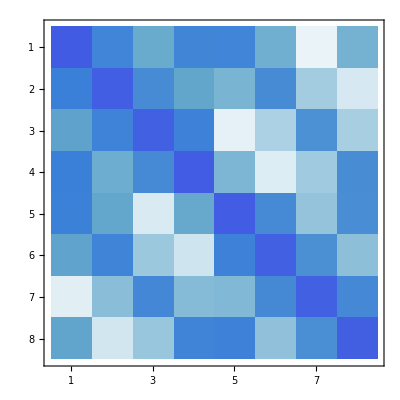

```mathematica
MatrixPlot[L]
```

```mathematica
xvec = LinearSolve[L,v]
```

{-0.26099,-0.0414596,-0.105931,-0.0414596,-0.163639,-0.12924,-0.134057,-0.12924}

```mathematica
chi[q_]:=Sum[
xvec[[i]] * Fo[q,oc[i],ow]
,{i,npoints}]
```

```mathematica
γ = Mean[Table[chi[sp[i]],{i,npoints}]];
```

```mathematica
ContourPlot3D[chi[{x,y,z}]==γ, {x, -1.50, 1.50}, {y, -1.50, 1.50},{z, -1.50, 1.50}]
```

-Graphics3D-